```mathematica
v=9;
l=5;
vv=ToString[v];
ll=ToString[l];
Chi1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-fine-1.txt",{Number,Number}];
Chit1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-fine-1.txt",{Number,Number}];
Chi2=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-fine-2.txt",{Number,Number}];
Chit2=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-fine-2.txt",{Number,Number}];
Chi3=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-fine-3.txt",{Number,Number}];
Chit3=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-fine-3.txt",{Number,Number}];
Chi4=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-fine-4.txt",{Number,Number}];
Chit4=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-fine-4.txt",{Number,Number}];

Chi5=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-fine-5.txt",{Number,Number}];
Chit5=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-fine-5.txt",{Number,Number}];
Chi6=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-fine-6.txt",{Number,Number}];
Chit6=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-fine-6.txt",{Number,Number}];
Chi7=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-fine-7.txt",{Number,Number}];
Chit7=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-fine-7.txt",{Number,Number}];
Chi8=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-fine-8.txt",{Number,Number}];
Chit8=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-fine-8.txt",{Number,Number}];

(*

Chi9=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-fine-9.txt",{Number,Number}];
Chit9=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-fine-9.txt",{Number,Number}];
Chi10=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-fine-10.txt",{Number,Number}];
Chit10=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-fine-10.txt",{Number,Number}];
Chi11=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-fine-11.txt",{Number,Number}];
Chit11=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-fine-11.txt",{Number,Number}];
Chi12=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-fine-12.txt",{Number,Number}];
Chit12=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-fine-12.txt",{Number,Number}];


Chiii[v][l]=Table[{Chi9[[All,1]][[i]],(Chi9[[All,2]][[i]]+Chi10[[All,2]][[i]]+Chi11[[All,2]][[i]]+Chi12[[All,2]][[i]])/4.},{i,1,Length[Chi9]}];
Chiiit[v][l]=Table[{Chit9[[All,1]][[i]],(Chit9[[All,2]][[i]]+Chit10[[All,2]][[i]]+Chit11[[All,2]][[i]]+Chit12[[All,2]][[i]])/4.},{i,1,Length[Chi9]}];
*)

Chi[v][l]=Table[{Chi1[[All,1]][[i]],(Chi1[[All,2]][[i]]+Chi2[[All,2]][[i]]+Chi3[[All,2]][[i]]+Chi4[[All,2]][[i]])/4.},{i,1,Length[Chi1]}];
Chit[v][l]=Table[{Chit1[[All,1]][[i]],(Chit1[[All,2]][[i]]+Chit2[[All,2]][[i]]+Chit3[[All,2]][[i]]+Chit4[[All,2]][[i]])/4.},{i,1,Length[Chi1]}];

Chii[v][l]=Table[{Chi5[[All,1]][[i]],(Chi5[[All,2]][[i]]+Chi6[[All,2]][[i]]+Chi7[[All,2]][[i]]+Chi8[[All,2]][[i]])/4.},{i,1,Length[Chi5]}];
Chiit[v][l]=Table[{Chit5[[All,1]][[i]],(Chit5[[All,2]][[i]]+Chit6[[All,2]][[i]]+Chit7[[All,2]][[i]]+Chit8[[All,2]][[i]])/4.},{i,1,Length[Chi5]}];




Ch4[v][l]={Chi[v][l][[1]]};
For [i=1, i<Length[Chii[v][l]], i++,
Ch4[v][l]=Append[Ch4[v][l],Chii[v][l][[i]]];
Ch4[v][l]=Append[Ch4[v][l],Chi[v][l][[i+1]]];
]
Ch4[v][l]=Append[Ch4[v][l],Chii[v][l][[Length[Chii[v][l]]]]];


Cht4[v][l]={Chit[v][l][[1]]};

For [i=1, i<Length[Chiit[v][l]], i++,
Cht4[v][l]=Append[Cht4[v][l],Chiit[v][l][[i]]];
Cht4[v][l]=Append[Cht4[v][l],Chit[v][l][[i+1]]];
]

Cht4[v][l]=Append[Cht4[v][l],Chiit[v][l][[Length[Chiit[v][l]]]]];

(* For [i=1,i<Length[Chiiit[v][l]]+1,i++,
Ch4[v][l]=Append[Ch4[v][l],Chiii[v][l][[i]]];
Cht4[v][l]=Append[Cht4[v][l],Chiiit[v][l][[i]]];] *)

Ch4[v][l]=Sort[Ch4[v][l],#1[[1]]<#2[[1]]&];
Cht4[v][l]=Sort[Cht4[v][l],#1[[1]]<#2[[1]]&];

i4[v][l]=Interpolation[Ch4[v][l]];
it4[v][l]=Interpolation[Cht4[v][l]];
```

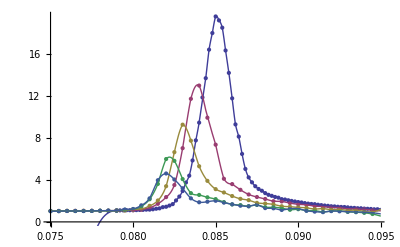

```mathematica
pic1=ListPlot[{Ch4[v][5],Ch4[v][10],Ch4[v][20],Ch4[v][50],Ch4[v][100]},PlotRange->Full];
pic2=Plot[{i4[v][5][i],i4[v][10][i],i4[v][20][i],i4[v][50][i],i4[v][100][i]},{i,0.075,0.095},PlotRange->Full];
Show[{pic1,pic2}]
```

```mathematica
----------------------------
```

0.011657  = val

0.065  = d0

0.5  = α

0.054  = z

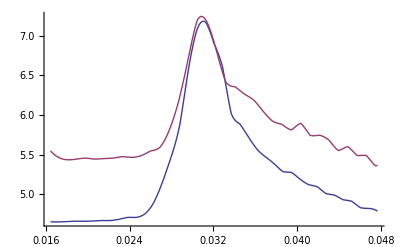

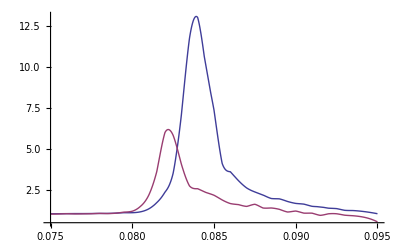

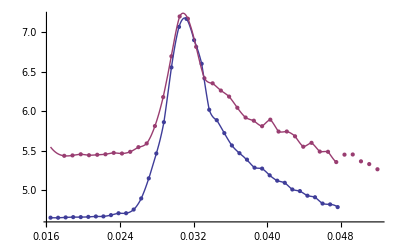

```mathematica
val=10000;
l1=10;
l2=50;


For[d0=0.065,d0<0.066,d0+=0.002,
For[z=0.0,z≤0.3,z+=0.002,
For[α=0.5,α≤0.5,α+=0.02,

x1[l1]=Table[{(x-d0)*(l1*1000.)^z,Log[i4[v][l1][x]]+α*Log[l1*1000.]},{x,0.075,0.094,0.0005}];
x1[l2]=Table[{(x-d0)*(l2*1000.)^z,Log[i4[v][l2][x]]+α*Log[l2*1000.]},{x,0.075,0.094,0.0005}];
ix1=Interpolation[x1[l1]];
ix2=Interpolation[x1[l2]];


min=Max[(0.075-d0)*(l1*1000.0)^z,(0.075-d0)*(l2*1000.0)^z];
max=Min[(0.095-d0)*(l1*1000.0)^z,(0.095-d0)*(l2*1000.0)^z];
delta=(max-min)/50;
int=Sum[(ix1[min+k*delta]-α*Log[l1*1000.]+ix2[min+k*delta]-α*Log[l2*1000.])*delta*(Max[ix1[min+k*delta],ix2[min+k*delta]]-Min[ix1[min+k*delta],ix2[min+k*delta]]),{k,0,50}];
If[int<val,
val=int;
d0f=d0;
αf=α;
zf=z;]
]
]
]

" = val"  val
" = d0" d0f
" = α" αf
" = z" zf

x1[l1]=Table[{(x-d0f)*(l1*1000.)^zf,Log[i4[v][l1][x]]+αf*Log[l1*1000.]},{x,0.075,0.094,0.0005}];
x1[l2]=Table[{(x-d0f)*(l2*1000.)^zf,Log[i4[v][l2][x]]+αf*Log[l2*1000.]},{x,0.075,0.094,0.0005}];
ix1=Interpolation[x1[l1]];
ix2=Interpolation[x1[l2]];
pic1=ListPlot[{x1[l1],x1[l2]},PlotRange->Full];
pic2=Plot[{ix1[x],ix2[x]},{x,Min[x1[l1][[All,1]][[1]],x1[l2][[All,1]][[1]]],Min[x1[l1][[All,1]][[Length[x1[l1]]]],x1[l2][[All,1]][[Length[x1[l1]]]]]},PlotRange->Full]
Plot[{i4[v][l1][x],i4[v][l2][x]},{x,0.075,0.095},PlotRange->Full]
Show[{pic1,pic2}]
```

0.011657  = val

0.07  = d0

0.5  = α

0.1  = z

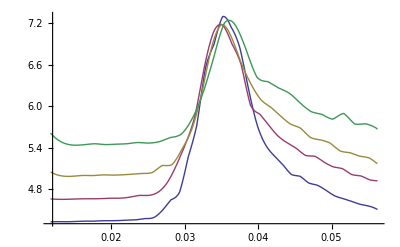

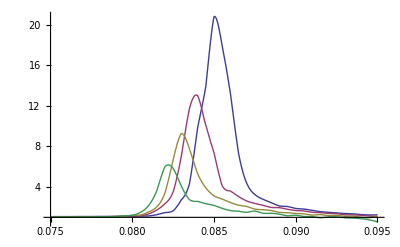

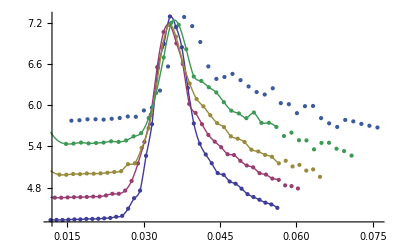

```mathematica
d0f=0.07;
αf=0.5;
zf=0.1;

l1=5;
l2=10;
l3=20;
l4=50;
l5=100;

" = val"  val
" = d0" d0f
" = α" αf
" = z" zf

x1[l1]=Table[{(x-d0f)*(l1*1000.)^zf,Log[i4[v][l1][x]]+αf*Log[l1*1000.]},{x,0.075,0.094,0.0005}];
x1[l2]=Table[{(x-d0f)*(l2*1000.)^zf,Log[i4[v][l2][x]]+αf*Log[l2*1000.]},{x,0.075,0.094,0.0005}];
x1[l3]=Table[{(x-d0f)*(l3*1000.)^zf,Log[i4[v][l3][x]]+αf*Log[l3*1000.]},{x,0.075,0.094,0.0005}];
x1[l4]=Table[{(x-d0f)*(l4*1000.)^zf,Log[i4[v][l4][x]]+αf*Log[l4*1000.]},{x,0.075,0.094,0.0005}];
x1[l5]=Table[{(x-d0f)*(l5*1000.)^zf,Log[i4[v][l5][x]]+αf*Log[l5*1000.]},{x,0.075,0.094,0.0005}];
ix1=Interpolation[x1[l1]];
ix2=Interpolation[x1[l2]];
ix3=Interpolation[x1[l3]];
ix4=Interpolation[x1[l4]];
ix5=Interpolation[x1[l5]];
pic1=ListPlot[{x1[l1],x1[l2],x1[l3],x1[l4],x1[l5]},PlotRange->Full];
pic2=Plot[{ix1[x],ix2[x],ix3[x],ix4[x]},{x,Min[x1[l1][[All,1]][[1]],x1[l2][[All,1]][[1]],x1[l3][[All,1]][[1]],x1[l4][[All,1]][[1]]],Min[x1[l1][[All,1]][[Length[x1[l1]]]],x1[l2][[All,1]][[Length[x1[l1]]]],x1[l3][[All,1]][[Length[x1[l3]]]],x1[l4][[All,1]][[Length[x1[l4]]]],x1[l5][[All,1]][[Length[x1[l5]]]]]},PlotRange->Full]
Plot[{i4[v][l1][x],i4[v][l2][x],i4[v][l3][x],i4[v][l4][x]},{x,0.075,0.095},PlotRange->Full]
Show[{pic1,pic2}]
```

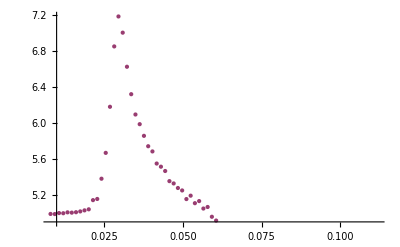
Show[{Plot[{i1[10][x],i1[20][x],i1[50][x],i1[100][x]},{x,chi[5]⟦All,1⟧⟦1⟧,chi[5]⟦All,1⟧⟦Length[chi[5]]⟧}],-Graphics-}]

0.072  = d0

0.5  = α

0.1  = z

```mathematica
v=9;
αf=0.5;
zf=0.1;
d0f=0.072;

Do[
chi1=Ch4[v][l][[All,1]];
chi2=Ch4[v][l][[All,2]];
chi[l]=Table[{(chi1[[i]]-d0f)*(l*1000.)^zf,
Log[chi2[[i]]]+αf*Log[l*1000.]},{i,1,Length[chi1]}];
i1[l]=Interpolation[chi[l]];
,{l,{5,10,20,50,100}}]

pic1=Plot[{i1[10][x],i1[20][x],i1[50][x],i1[100][x]},{x,chi[5][[All,1]][[1]],chi[5][[All,1]][[Length[chi[5]]]]}];

pic2=ListPlot[{chi[10],chi[20],chi[50],chi[100]}];

Show[{pic1,pic2}]


" = d0" d0f
" = α" αf
" = z" zf
```

```mathematica
-----------------------
```

-0.103145  = val

0.057  = d0

0.45  = α

0.16  = z

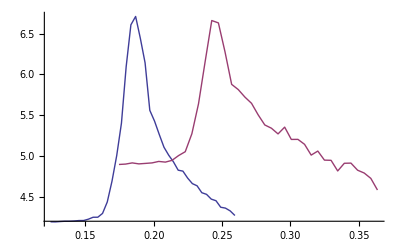

```mathematica
v=9;
l1=10;
l2=50;
j=0;
l=0.075+j*0.0005;
val=10000;

Chi11=Ch4[v][l1][[All,1]];
Chi12=Ch4[v][l1][[All,2]];
Chi21=Ch4[v][l2][[All,1]];
Chi22=Ch4[v][l2][[All,2]];

For[d0=0.045,d0<0.075,d0+=0.001,
For[z=0.08,z≤0.2,z+=0.01,
For[α=0.45,α≤0.65,α+=0.02,

j=1;
While[Chi11[[j]]<d0,j++];
(*Chil1=Table[{Log[Chi11[[i]]-d0]+z*Log[l1*1000.],
Log[Chi12[[i]]]+α*Log[l1*1000.]},{i,j,Length[Chi11]}];
Chil2=Table[{Log[Chi21[[i]]-d0]+z*Log[l2*1000.],
Log[Chi22[[i]]]+α*Log[l2*1000.]},{i,j,Length[Chi21]}];*)

Chil1=Table[{(Chi11[[i]]-d0)*(l1*1000.)^z,
Log[Chi12[[i]]]+α*Log[l1*1000.]},{i,j,Length[Chi11]}];
Chil2=Table[{(Chi21[[i]]-d0)*(l2*1000.)^z,
Log[Chi22[[i]]]+α*Log[l2*1000.]},{i,j,Length[Chi21]}];

i1=Interpolation[Chil1];
i2=Interpolation[Chil2];

(*min=Max[Log[Chi11[[j]]-d0]+z*Log[l1*1000.],Log[Chi21[[j]]-d0]+z*Log[l2*1000.]];
max=Min[Log[Chi11[[Length[Chi11]]]-d0]+z*Log[l1*1000.],Log[Chi21[[Length[Chi11]]]-d0]+z*Log[l2*1000.]];*)


min=Max[(Chi11[[i]]-d0)*(l1*1000.)^z,(Chi21[[i]]-d0)*(l2*1000.)^z];
max=Min[(Chi11[[Length[Chi11]]]-d0)*(l1*1000.)^z,(Chi21[[Length[Chi11]]]-d0)*(l2*1000.)^z];


delta=(max-min)/50;
int=Sum[
Log[(i2[min+k*delta]-(l2*1000.)^z)*(i1[min+k*delta]-(l1*1000.)^z)]*delta*(Max[i1[min+k*delta],i2[min+k*delta]]-Min[i1[min+k*delta],i2[min+k*delta]]),{k,0,50}];
If[int<val,
val=int;
d0f=d0;
αf=α;
zf=z;]
]
]
]

" = val"  val
" = d0" d0f
" = α" αf
" = z" zf

Chil1=Table[{(Chi11[[i]]-d0f)*(l1*1000.)^z,
Log[Chi12[[i]]]+αf*Log[l1*1000.]},{i,1,Length[Chi11]}];
Chil2=Table[{(Chi21[[i]]-d0f)*(l2*1000.)^z,
Log[Chi22[[i]]]+αf*Log[l2*1000.]},{i,1,Length[Chi21]}];

ListLinePlot[{Chil1,Chil2}]
```

```mathematica
------------------------------------
```

```mathematica
v=9;
l=50;
vv=ToString[v];
ll=ToString[l];
Chi1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-1.txt",{Number,Number}];
Chit1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-1.txt",{Number,Number}];
Chi2=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-2.txt",{Number,Number}];
Chit2=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-2.txt",{Number,Number}];
Chi3=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-3.txt",{Number,Number}];
Chit3=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-3.txt",{Number,Number}];
Chi4=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-4.txt",{Number,Number}];
Chit4=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-4.txt",{Number,Number}];

Chi5=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-5.txt",{Number,Number}];
Chit5=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-5.txt",{Number,Number}];
Chi6=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-6.txt",{Number,Number}];
Chit6=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-6.txt",{Number,Number}];
Chi7=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-7.txt",{Number,Number}];
Chit7=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-7.txt",{Number,Number}];
Chi8=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-8.txt",{Number,Number}];
Chit8=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-8.txt",{Number,Number}];



Chi9=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-9.txt",{Number,Number}];
Chit9=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-9.txt",{Number,Number}];
Chi10=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-10.txt",{Number,Number}];
Chit10=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-10.txt",{Number,Number}];
(*Chi11=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-fine-11.txt",{Number,Number}];
Chit11=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-fine-11.txt",{Number,Number}];
Chi12=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-fine-12.txt",{Number,Number}];
Chit12=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-fine-12.txt",{Number,Number}];


Chiii[v][l]=Table[{Chi9[[All,1]][[i]],(Chi9[[All,2]][[i]]+Chi10[[All,2]][[i]]+Chi11[[All,2]][[i]]+Chi12[[All,2]][[i]])/4.},{i,1,Length[Chi9]}];
Chiiit[v][l]=Table[{Chit9[[All,1]][[i]],(Chit9[[All,2]][[i]]+Chit10[[All,2]][[i]]+Chit11[[All,2]][[i]]+Chit12[[All,2]][[i]])/4.},{i,1,Length[Chi9]}];
*)

(*Chi[v][l]=Table[{Chi1[[All,1]][[i]],(Chi1[[All,2]][[i]]+Chi2[[All,2]][[i]]+Chi3[[All,2]][[i]]+Chi4[[All,2]][[i]]+Chi5[[All,2]][[i]]+Chi1[[All,2]][[i+1]]+Chi2[[All,2]][[i+1]]+Chi3[[All,2]][[i+1]]+Chi4[[All,2]][[i+1]]+Chi5[[All,2]][[i+1]])/10.},{i,1,Length[Chi1],2}];*)
Chi[v][l]=Table[{Chi1[[All,1]][[i]],(Chi1[[All,2]][[i]]+Chi2[[All,2]][[i]]+Chi3[[All,2]][[i]]+Chi4[[All,2]][[i]]+Chi5[[All,2]][[i]]+Chi6[[All,2]][[i]]+Chi7[[All,2]][[i]]+Chi8[[All,2]][[i]]+Chi9[[All,2]][[i]]+Chi10[[All,2]][[i]])/10.},{i,1,Length[Chi1]}];
Chit[v][l]=Table[{Chit1[[All,1]][[i]],(Chit1[[All,2]][[i]]+Chit2[[All,2]][[i]]+Chit3[[All,2]][[i]]+Chit4[[All,2]][[i]]+Chit5[[All,2]][[i]]+Chit6[[All,2]][[i]]+Chit7[[All,2]][[i]]+Chit8[[All,2]][[i]]+Chit9[[All,2]][[i]]+Chit10[[All,2]][[i]])/10.},{i,1,Length[Chi1]}];







Cht4[v][l]=Chit[v][l];
Ch4[v][l]=Chi[v][l];

(* For [i=1,i<Length[Chiiit[v][l]]+1,i++,
Ch4[v][l]=Append[Ch4[v][l],Chiii[v][l][[i]]];
Cht4[v][l]=Append[Cht4[v][l],Chiiit[v][l][[i]]];] *)



i4[v][l]=Interpolation[Ch4[v][l]];
it4[v][l]=Interpolation[Cht4[v][l]];
```

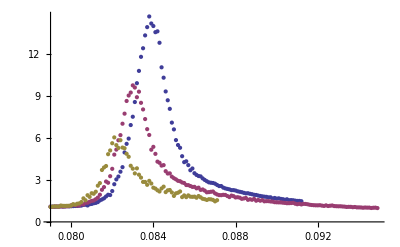

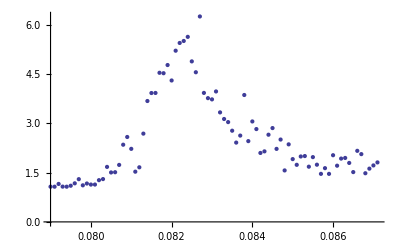

```mathematica
ListPlot[{Chi[9][10],Chi[9][20],Chi[9][50]},PlotRange->Full]
ListPlot[{Chi9},PlotRange->Full]
```

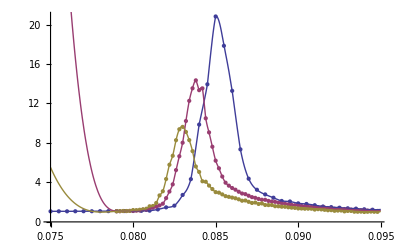

```mathematica
pic1=ListPlot[{Ch4[v][5],Ch4[v][10],Ch4[v][20]},PlotRange->Full];
pic2=Plot[{i4[v][5][i],i4[v][10][i],i4[v][20][i]},{i,0.075,0.095},PlotRange->Full];
Show[{pic1,pic2}]
```

```mathematica
Ch4[9][10]
```

{{0.079,1.08361},{0.0792,1.08221},{0.0794,1.09879},{0.0796,1.09897},{0.0798,1.11687},{0.08,1.11889},{0.0802,1.13564},{0.0804,1.15287},{0.0806,1.24659},{0.0808,1.2118},{0.081,1.33913},{0.0812,1.43504},{0.0814,1.55098},{0.0816,1.66961},{0.0818,1.84374},{0.082,2.40803},{0.0822,3.07628},{0.0824,3.80379},{0.0826,5.25043},{0.0828,6.65349},{0.083,8.02397},{0.0832,10.2254},{0.0834,12.2685},{0.0836,13.5409},{0.0838,14.3464},{0.084,13.349},{0.0842,13.5341},{0.0844,10.4991},{0.0846,9.07008},{0.0848,7.61671},{0.085,6.2076},{0.0852,5.43036},{0.0854,4.59592},{0.0856,3.97237},{0.0858,3.67187},{0.086,3.4347},{0.0862,3.26297},{0.0864,3.0567},{0.0866,2.87675},{0.0868,2.81279},{0.087,2.65159},{0.0872,2.51112},{0.0874,2.43829},{0.0876,2.32935},{0.0878,2.24477},{0.088,2.23904},{0.0882,2.12621},{0.0884,2.07196},{0.0886,2.03313},{0.0888,1.9504},{0.089,1.89583},{0.0892,1.84811},{0.0894,1.77436},{0.0896,1.73251},{0.0898,1.69241},{0.09,1.68759},{0.0902,1.61857},{0.0904,1.58526},{0.0906,1.55323},{0.0908,1.52712},{0.091,1.50102},{0.0912,1.46327},{0.0914,1.46096},{0.0916,1.44973},{0.0918,1.40851},{0.092,1.38026},{0.0922,1.33209},{0.0924,1.32651},{0.0926,1.3092},{0.0928,1.3044},{0.093,1.27351},{0.0932,1.24869},{0.0934,1.22452},{0.0936,1.21012},{0.0938,1.18139},{0.094,1.17269},{0.0942,1.14849},{0.0944,1.13267},{0.0946,1.10929},{0.0948,1.10891}}

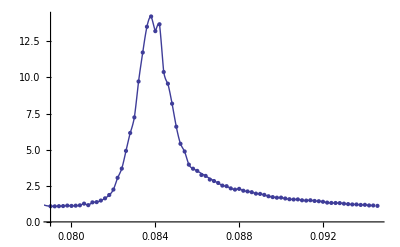

```mathematica
pic1=ListPlot[{Ch4[v][10]},PlotRange->Full];
pic2=Plot[{i4[v][10][i]},{i,0.075,0.095},PlotRange->Full];
Show[{pic1,pic2}]
```